# Machine learning test

```mathematica
SystemOpen@$UserBaseDirectory
```

## Setup

```mathematica
<<LatticePlane`
```

```mathematica
(*SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo"]
AbsoluteTiming@DensityHKL["mp-134"]*)
```

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[_, _]]//Once
```

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo"]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\epdo

```mathematica
data=Import["stable_elasticity_mp-ids.csv"];
{mpids,Subscript[K, VRH]}=data⟦2;;⟧ᵀ;
```

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo\\cif\\stable_elastic"]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\epdo\cif\stable_elastic

```mathematica
SeedRandom[10];
rc=RandomChoice[Range@Length@mpids,1000];
mpidsRand=mpids⟦rc⟧;
Subscript[K, VRH,rand]=Subscript[K, VRH]⟦rc⟧;
```

```mathematica
Clear@DensityHKLtmp
n=3;
hklMax=3;
dFactor=1.;
rFactor=1;
method="HardSphere";
DensityHKLtmp[i_]:=DensityHKL[mpids⟦i⟧,n,hklMax,dFactor,rFactor,"Method"->method,"PrintID"->False]
```

```mathematica
splits=Partition[Range@Length@mpids,UpTo@100];
splits=splits⟦27;;⟧;
```

## ParallelDo

```mathematica
ParallelNeeds["LatticePlane`"]
```

```mathematica
Do[{t,results}=AbsoluteTiming@ParallelMap[DensityHKL[#,n,hklMax,dFactor,rFactor,"Method"->method,"PrintID"->False]&,mpids⟦split⟧];Print@t;DumpSave[FileNameJoin@{"..","..","density-hkl","stable-elastic","n3_maxHKL3_dFactor1_rFactor1","hkl_"<>ToString@split⟦1⟧<>"-"<>ToString@split⟦-1⟧<>".mx"},results],
{split,splits}
]
```

$Aborted

```mathematica
(*ParallelMap[DensityHKL[#,n,hklMax,dFactor,rFactor,"Method"->method,"PrintID"->False]&,{"mp-11819","mp-11918"}]*)
```

## ParallelDo

```mathematica
ParallelDo[Print@{i⟦1⟧,i⟦-1⟧};results=(DensityHKLtmp/@i)ᵀ;(*DumpSave[FileNameJoin@{"..","..","density-hkl","stable-elastic","hkl_"<>ToString@i⟦1⟧<>"-"<>ToString@i⟦-1⟧<>".mx"},{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}]*),{i,splits}];
```

```mathematica
argv=Rest@$ScriptCommandLine;
i=argv⟦1⟧;
data=Import["stable_elasticity_mp-ids.csv"];
{mpids,Kvrh}=data⟦2;;⟧ᵀ;
splits=Partition[Range@Length@mpids,UpTo@100];
split=splits⟦i⟧;
SetDirectory["cif/stable_elastic"]
results=DensityHKL[#,n=1,hklMax=3,dFactor=0.1,rFactor=1,"Method"->"HardSphere","PrintID"->False]&/@split;
DumpSave[FileNameJoin@{"..","..","density-hkl","stable-elastic","hkl_"<>ToString@split⟦1⟧<>"-"<>ToString@split⟦-1⟧<>".mx"},results] (*{Aoutn,AoutCt,hklList,Afulln,AfullCt,hklFull,EUnique}*)
```

```mathematica
Do[{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=(ResourceFunction["MonitorProgress"][DensityHKLtmp/@i])ᵀ;DumpSave[FileNameJoin@{"..","..","density-hkl","stable-elastic","hkl_"<>ToString@i⟦1⟧<>"-"<>ToString@i⟦-1⟧<>".mx"},{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}],{i,splits}];
```

```mathematica
(*<<(FileNameJoin@{"..","..","density-hkl","stable-elastic","hkl_"<>ToString@splits⟦1,1⟧<>"-"<>ToString@splits⟦1,-1⟧<>".mx"})*)
```

```mathematica
(*??Global`**)
```

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo\\density-hkl\\stable-elastic"]
```

C:\Users\sterg\Documents\GitHub\sparks-baird\epdo\density-hkl\stable-elastic

```mathematica
Do[fileName=(FileNameJoin@{"hkl_"<>ToString@split⟦1⟧<>"-"<>ToString@split⟦-1⟧<>".mx"});<<(fileName);results={𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}ᵀ;DumpSave[fileName,results];,{split,splits⟦;;15⟧}];
```

Keys::invrl: The argument {1,4} is not a valid Association or a list of rules.

Values::invrl: The argument {{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»} is not a valid Association or a list of rules.

Keys::invrl: The argument 0. is not a valid Association or a list of rules.

Values::invrl: The argument {0.,0.0553101,0.189187,0.,0.,0.,0.109582,0.,0.14336,0.,«77»} is not a valid Association or a list of rules.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},«3»,{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Keys[{«1»}],Values[{0.,0.0553101,0.189187,0.,0.,0.,0.109582,0.,0.14336,0.,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Keys::invrl: The argument {1,4} is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Values::invrl: The argument {{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»} is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},«8»,«542»}],Keys[{«20»,«9»,«77»}],Values[{0.245585,0.0720556,0.,0.0691472,0.,0.260354,0.142419,0.244957,0.18608,0.106686,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{«1»},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],«1»,Values[{0.,0.0120648,0.,0.,0.,0.,0.,0.,0.,0.030347,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
resultsFull={};
Do[<<(FileNameJoin@{"hkl_"<>ToString@split⟦1⟧<>"-"<>ToString@split⟦-1⟧<>".mx"});resultsFull=Join[resultsFull,results];,{split,splits}];
```

Keys::invrl: The argument {1,4} is not a valid Association or a list of rules.

Values::invrl: The argument {{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»} is not a valid Association or a list of rules.

Keys::invrl: The argument 0. is not a valid Association or a list of rules.

Values::invrl: The argument {0.,0.0553101,0.189187,0.,0.,0.,0.109582,0.,0.14336,0.,«77»} is not a valid Association or a list of rules.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},«3»,{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Keys[{«1»}],Values[{0.,0.0553101,0.189187,0.,0.,0.,0.109582,0.,0.14336,0.,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Keys::invrl: The argument {1,4} is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Values::invrl: The argument {{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»} is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},«8»,«542»}],Keys[{«20»,«9»,«77»}],Values[{0.245585,0.0720556,0.,0.0691472,0.,0.260354,0.142419,0.244957,0.18608,0.106686,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argrx: Rule called with 4 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

ReplaceAll::reps: {Rule[Keys[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{10,14,17,23,49,54},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],Values[{{1,4},{2,3,5,6,18,22},{7,13},{8,15,19,21,45,58},{9,12,16,20,95,109},{«1»},{11,24,44,46,52,55},{25,35},{26,38,48,53,94,118},{27,40,47,51,175,210},«542»}],«1»,Values[{0.,0.0120648,0.,0.,0.,0.,0.,0.,0.,0.030347,«77»}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

## Export to HDF5 Format

```mathematica
(*fname=FileNameJoin@{"n1_maxHKL4_dFactor100m_rFactor1","1-12420.hdf5"};*)
```

```mathematica
(*{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=resultsFullᵀ;
Export[fname,{"AtomicPackingFraction"->{"Data"->𝒜outn},"AtomsPer}];*)
```

## Training Setup

```mathematica
𝒜size=Dimensions[𝒜fullCt⟦1,1⟧]⟦1⟧;
```

```mathematica
(*{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=Flatten[resultsFull,{1,3}]ᵀ;*)
```

```mathematica
{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=resultsFullᵀ;
```

```mathematica
d=Length/@Dimensions/@𝒜fullCt;
errPos=Position[d,1];(*it should have 2 dimensions*)
{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=Delete[#,errPos]&/@{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique};
ℰkeys=ℰUnique//Flatten//DeleteDuplicates
```

{Tm,Tl,Te,Fe,H,Ta,B,Hf,Zn,Au,Cu,Ni,N,Ti,Ag,La,Bi,Pt,Sc,Yb,Dy,Al,Th,Sb,Se,In,Lu,Ir,Er,Ge,U,C,Ho,Cs,Ca,Cl,P,Cd,As,Mn,F,Zr,Y,Cr,Sr,W,Rb,Li,V,Be,Nb,Co,Si,Sn,Ga,Rh,Sm,S,K,Re,Mg,Ba,Hg,Tb,Mo,Pr,Pd,O,Ce,Na,Nd,Eu,Gd,Pb,I,Br,Tc,Os,Ru,Pa,Ac,Pm,Pu,Np,Ar,Kr,He,Ne,Xe}

## Stack Values into 3D Matrix after Adding

```mathematica
n=2;
X=(Normal[SparseArray[hklFull⟦1⟧+(n+1)->#]]&/@#)&/@𝒜fullCt;
X=Total[X,{2}];
```

## Regular List

```mathematica
X=Standardize/@Total[𝒜fullCt,{2}];
```

## Sorted List

```mathematica
X=Standardize/@Total[𝒜fullCt,{2}];
X=ReverseSort/@X;
method="Sorted, Summed List";
```

## Add Domain Knowledge (Element Properties)

```mathematica
props=ElementData["Properties"]
```

{Abbreviation,AdiabaticIndex,AllotropeNames,AllotropicMultiplicities,AlternateNames,AlternateStandardNames,AtomicMass,AtomicNumber,AtomicRadius,Block,BoilingPoint,BrinellHardness,BulkModulus,CASNumber,Color,CommonCompoundNames,CovalentRadius,CriticalPressure,CriticalTemperature,CrustAbundance,CrystalStructure,CuriePoint,DecayMode,Density,DiscoveryCountries,DiscoveryYear,ElectricalConductivity,ElectricalType,ElectronAffinity,ElectronConfiguration,ElectronConfigurationString,Electronegativity,ElectronShellConfiguration,FusionHeat,GasAtomicMultiplicities,Group,HalfLife,HumanAbundance,IconColor,IonizationEnergies,IsotopeAbundances,KnownIsotopes,LatticeAngles,LatticeConstants,Lifetime,LiquidDensity,MagneticType,MassMagneticSusceptibility,MeltingPoint,Memberships,MeteoriteAbundance,MohsHardness,MolarMagneticSusceptibility,MolarVolume,Name,NeelPoint,NeutronCrossSection,NeutronMassAbsorption,OceanAbundance,Period,Phase,PoissonRatio,QuantumNumbers,Radioactive,RefractiveIndex,Resistivity,Series,ShearModulus,SolarAbundance,SoundSpeed,SpaceGroupName,SpaceGroupNumber,SpecificHeat,StableIsotopes,StandardName,SuperconductingPoint,ThermalConductivity,ThermalExpansion,UniverseAbundance,UnstableIsotopes,Valence,VanDerWaalsRadius,VaporizationHeat,VickersHardness,VolumeMagneticSusceptibility,YoungModulus}

```mathematica
(*props={"AtomicMass","AtomicNumber","AtomicRadius","BoilingPoint","BrinellHardness","BulkModulus","CovalentRadius","CriticalPressure","CriticalTemperature","CrustAbundance","CuriePoint","Density","ElectricalConductivity","ElectronAffinity","Electronegativity","FusionHeat","HalfLife","HumanAbundance",(*"IonizationEnergies",*)(*"IsotopeAbundances",*)"LatticeAngles","LatticeConstants","Lifetime","LiquidDensity","MassMagneticSusceptibility","MeltingPoint","MohsHardness","MolarMagneticSusceptibility","MolarVolume","NeelPoint","NeutronCrossSection","NeutronMassAbsorption","PoissonRatio","SpecificHeat","SuperconductingPoint","ThermalConductivity","ThermalExpansion","Valence","VanDerWaalsRadius","VaporizationHeat","VickersHardness","VolumeMagneticSusceptibility","YoungModulus"};*)
(*props={"AtomicMass","AtomicRadius","BoilingPoint","BrinellHardness","BulkModulus","CovalentRadius","CrustAbundance","Density","ElectricalConductivity","ElectronAffinity","Electronegativity","FusionHeat"(*,"LatticeAngles","LatticeConstants"*),"LiquidDensity","MassMagneticSusceptibility","MeltingPoint","MohsHardness","MolarMagneticSusceptibility","MolarVolume","NeelPoint","NeutronMassAbsorption","PoissonRatio","SpecificHeat","SuperconductingPoint","ThermalConductivity","ThermalExpansion","Valence","VanDerWaalsRadius","VaporizationHeat","VolumeMagneticSusceptibility","YoungModulus"};*)
props={"CovalentRadius","MeltingPoint","Density","MolarVolume","AtomicNumber","Electronegativity"};
```

```mathematica
ℰfull=ElementData[#,"Abbreviation"]&/@Range@118;
```

```mathematica
elementData=Table[ElementData[i,j],{i,ℰfull},{j,props}];
```

```mathematica
(*ids=Position[props,#]&/@{"LatticeAngles","LatticeConstants"}//Flatten;*)
```

```mathematica
elementData=SynthesizeMissingValues[elementData];
```

```mathematica
elementDataStandard=Standardize/@QUC@elementData;
```

```mathematica
elemRules=MapThread[#1->#2&,{ℰfull,elementDataStandard}];
```

```mathematica
X1=(*ReverseSort/@*)𝒜fullCt;
```

```mathematica
rules1=Thread[ℰfull->elementDataStandard];
X2=ℰUnique/.rules1;
```

```mathematica
ElementMultiply[x_,y_]:=Flatten@(Total[x #&/@(yᵀ),{2}]/(Length@x)) (*Total[x #&/@(yᵀ),{1}]/(Length@x)*)
```

```mathematica
X=MapThread[ElementMultiply[#1,#2]&,{X1,X2}];
Dimensions@X
```

{12304,2052}

```mathematica
(*X=DimensionReduce[X,6];*)
```

## Composition Only

```mathematica
SetDirectory["C:\\Users\\sterg\\Documents\\GitHub\\sparks-baird\\epdo"]
data=Import["stable_props.csv","Dataset",HeaderLines->1];
```

C:\Users\sterg\Documents\GitHub\sparks-baird\epdo

```mathematica
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"C:\\Users\\sterg\\anaconda3"] (*for python executable*)
SetEnvironment["PATH"->Environment["PATH"]<>";"<>"C:\\Users\\sterg\\anaconda3\\Library\\bin"] (*for pyzmq library*)
RegisterExternalEvaluator["Python","C:\\Users\\sterg\\anaconda3\\python.exe"]
```

4704a274-218e-4a4b-933c-5781780f404c

```mathematica
formulasFull=Normal@data⟦;;,"unit_cell_formula"⟧;
formulasFull="["<>(#<>","&/@formulasFull)<>"]";
formulasFull=ImportString[formulasFull,"PythonExpression"];
```

```mathematica
mpidsFull=Normal@data⟦;;,"task_id"⟧;
```

```mathematica
assoc=Association@Thread[mpidsFull->formulasFull];
```

```mathematica
mpids2=Delete[mpids⟦Flatten@splits⟧,errPos];
formulas=Values@assoc⟦mpids2⟧;
```

```mathematica
X=((Keys@#/.elemRules)ᵀ.(Values@#))/(Total@Values@#)&/@formulas;
```

## Fill Element List with Matrices (and Zero Matrices)

```mathematica
(*X=Delete[𝒜fullCt,errPos];*)
rules1=MapThread[Thread[#1->#2]&,{ℰ,𝒜fullCt}];
rules2=#->ConstantArray[0,𝒜size]&/@Complement[ℰkeys,#]&/@ℰ;
X=MapThread[Flatten[ℰkeys/.#1/.#2]&,{rules1,rules2}];
```

## Fill with Zero Matrices up to n-th Matrix, Also Pass Nominal Vector of Elements

```mathematica
L=Length/@ℰUnique;
Subscript[L, max]=Max@L
```

6

```mathematica
ℰUniqueFilled=MapThread[#1~Join~ConstantArray["None",Subscript[L, max]-#2]&,{ℰUnique,L}];
```

```mathematica
(*rules1=MapThread[Thread[#1->#2]&,{ℰUnique,𝒜fullCt}];*)
rules1=MapThread[Thread[#1->ReverseSort/@#2]&,{ℰUnique,𝒜fullCt}];
rules2="None"->ConstantArray[0,Dimensions@𝒜fullCt⟦1,1⟧];
```

```mathematica
X=MapThread[{#1/.#2/.rules2,#1}&,{ℰUniqueFilled,rules1}];
```

```mathematica
X⟦;;,1⟧=Flatten@#&/@X⟦;;,1⟧;
```

```mathematica
Dimensions@X
```

{12304,2}

## Max Lattice Plane Density

```mathematica
max=Map[Max,𝒜fullCt,{2}];
```

```mathematica
rules1=MapThread[Thread[#1->#2]&,{ℰUnique,max}];
rules2="None"->0;
```

```mathematica
X=MapThread[{#1/.#2/.rules2,#1}&,{ℰUniqueFilled,rules1}];
```

```mathematica
X⟦1⟧
```

{{0.0589742,0.0589742,0.0323309,0,0,0},{Tm,Tl,Te,None,None,None}}

## Top Lattice Plane Densities

```mathematica
flat=ReverseSort/@Flatten[#ᵀ,{2}]&/@𝒜outCt; (*just take unique values*)
Subscript[L, top]=3;
top=Map[#⟦1;;Subscript[L, top]⟧&,flat,{2}];
```

```mathematica
rules1=MapThread[Thread[#1->#2]&,{ℰUnique,top}];
rules2="None"->ConstantArray[0,Subscript[L, top]];
```

```mathematica
X=MapThread[{#1/.#2/.rules2,#1}&,{ℰUniqueFilled,rules1}];
```

```mathematica
X⟦1⟧
```

{{{0.0589742,0.0289094,0.023147},{0.0589742,0.0555114,0.0306249},{0.0323309,0.0239023,0.0163186},{0,0,0},{0,0,0},{0,0,0}},{Tm,Tl,Te,None,None,None}}

## Composition, no domain knowledge

```mathematica
X=MapThread[{(#1/.#2/."None"->0)/(Total@Values@#2),#1}&,{ℰUniqueFilled,formulas}];
```

```mathematica
ids=Position[Head/@Flatten@X⟦;;,1⟧,Except[Real],Heads->False]/Subscript[L, max]//Flatten//N//Round;(*some of the formulas don't match ℰUnique*)
```

```mathematica
X⟦ids⟧=ConstantArray[0,{Length@ids,Sequence@@Dimensions@X⟦1⟧}]; (*effectively remove data*)
```

```mathematica
Dimensions@X
```

{12304,2,6}

## Composition & Planar Density

```mathematica
rules1=MapThread[Thread[#1->ReverseSort/@Flatten/@#2]&,{ℰUnique,𝒜fullCt}];
rules2="None"->ConstantArray[0,Dimensions@𝒜fullCt⟦1,1⟧];
```

```mathematica
Subscript[X, tmp]=MapThread[{(#1/.#2/."None"->0)/(Total@Values@#2),#1}&,{ℰUniqueFilled,formulas}];
```

```mathematica
X=MapThread[{#1⟦2⟧/.#2/.rules2,Sequence@@#1}&,{Subscript[X, tmp],rules1}];
```

```mathematica
X⟦1,1⟧//Dimensions
```

{6,342}

## Just Elements

```mathematica
X=ℰUniqueFilled;
```

## Just Elements, One-Hot

```mathematica
rules1=Thread[#1->1]&/@ℰUnique;
rules2=#->0&/@Complement[ℰkeys,#]&/@ℰUnique;
X=MapThread[Flatten[ℰkeys/.#1/.#2]&,{rules1,rules2}];
```

## One-Hot Composition

```mathematica
rules=#->0&/@Complement[ℰfull,#]&/@Keys@formulas;
X=MapThread[Flatten[ℰfull/(Total@Values@#1)/.#1/.#2]&,{formulas,rules}];
```

```mathematica
(*ids=Position[Head/@Flatten@X,Except[Real],Heads->False]/118//Flatten//N//Round;(*some of the formulas don't match ℰUnique*)*)
(*X⟦ids⟧=ConstantArray[0,{Length@ids,118}];*)
```

## Other

```mathematica
(*X=Total[Delete[𝒜fullCt,errPos],{2}];(*maybe better than 𝒜outn*)*)
(*X=MapThread[{#1,#2}ᵀ&,{𝒜fullCt,ℰUnique}];*)
```

## Utility Function

```mathematica
utility[a_,p_]:=-Piecewise[{{Exp[p-a],a<p},{Exp[3*(a-p)],a≥p}}] (*causes very slow data pre-processing*)
```

Plot this function for a given actual value:

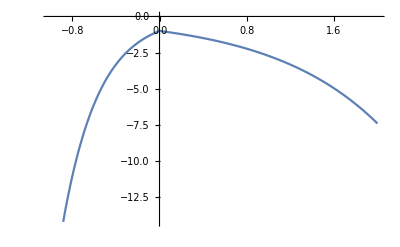

```mathematica
Plot[utility[0,p],{p,-1,2}]
```

## Target Value, Train/Val/Test Splits, and Predictions

```mathematica
TrainTestSplit=ResourceFunction["TrainTestSplit"]
```

```mathematica
y=Delete[Subscript[K, VRH]⟦Flatten@splits⟧,errPos];
(*y=Log10[Delete[Subscript[K, VRH]⟦Flatten@splits⟧,errPos]]/.Indeterminate->0;*)(*maybe I should do the Subscript[Log, 10] after training (i.e. for error calculation)*)
(*y=y /. 0.->1.;(*to avoid issue with Log10*)*)
SeedRandom[11];
{trainValidation,test}=TrainTestSplit[Thread[X->y]ᵀ,"TrainingSetSize"->0.9];
(*trainValidation=Sort[trainValidation,Values@#1<Values@#2&];*)
{train,validation}=TrainTestSplit[trainValidation,"TrainingSetSize"->0.7/0.9,"Shuffle"->False];
(*train=Sort[train,Values@#1<Values@#2&];*)
(*{train1,train2}=TrainTestSplit[train,"TrainingSetSize"->0.8,"Shuffle"->False];*)
```

```mathematica
p=Predict[train,PerformanceGoal->"Quality"(*,"ValidationSet"->train2*)(*"Quality"*),TargetDevice->"GPU"(*,"Method"->"NearestNeighbors"*)(*,FeatureExtractor->"IndicatorVector"*)(*,"Method"->"NeuralNetwork"*)(*,TimeGoal->60*)(*,"UtilityFunction"->utility*)];
```

```mathematica
Mean@Abs[Subscript[K, VRH]-Mean@Subscript[K, VRH]]
```

57.1378

```mathematica
MAE[x_,y_]:=Mean@Abs[x-y]
SelfMAE[x_]:=MAE[x,Mean@x]
```

```mathematica
Subscript[y, train]=Values@train;
trainSelfMAE=SelfMAE@Subscript[y, train];
Subscript[y, train,log]=Log10@Subscript[y, train]/.Indeterminate->0;
trainSelfLogMAE=SelfMAE@Subscript[y, train,log];
```

```mathematica
Subscript[y, validation]=Values@validation;
Subscript[y, validation,pred]=p[Keys@validation];
validationMAE=MAE[Subscript[y, validation],Subscript[y, validation,pred]];
dummyMAE=MAE[Subscript[y, validation],Mean@Subscript[y, train]];
```

```mathematica
scaledError=validationMAE/dummyMAE
```

0.572941

```mathematica
Subscript[y, validation,log]=Log10@Subscript[y, validation]/.Indeterminate->0;
Subscript[y, validation,pred,log]=Log10@p[Keys@validation]/.Indeterminate->0;
```

```mathematica
validationLogMAE=MAE[Subscript[y, validation,log],Subscript[y, validation,pred,log]];
dummyLogMAE=MAE[Subscript[y, validation,log],Mean@Subscript[y, train,log]];
```

```mathematica
scaledLogError=validationLogMAE/dummyLogMAE
```

0.638683

```mathematica
pm=PredictorMeasurements[p,#,ComputeUncertainty->True]&/@{train,validation};
```

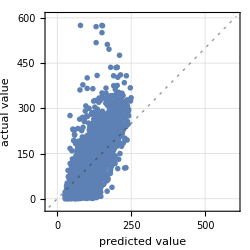
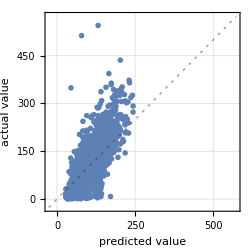
Model | Training | Validation
Predictor information
Data type | {NumericalTensor (××63),NominalVector (6)}
Standard deviation | 45.8 ± 1.6
Method | GradientBoostedTrees
Single evaluation time | 4.67 ms/example
Batch evaluation speed | 23.9 examples/ms
Loss | 5.26 ± 0.042
Model memory | 672. kB
Training examples used | 8613 examples
Training time | 6.74 s
 |  | Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 8613
Standard deviation | 43.5 ± 0.83
Standard deviation baseline | 71.1 ± 0.76
R-squared | 0.625 ± 0.016
Mean cross entropy | 5.19 ± 0.019
Single evaluation time | 5.16 ms/example
Batch evaluation speed | 1.96 examples/ms
-Graphics- |  | Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 2461
Standard deviation | 44.9 ± 1.5
Standard deviation baseline | 70.2 ± 1.4
R-squared | 0.591 ± 0.031
Mean cross entropy | 5.23 ± 0.036
Single evaluation time | 5.13 ms/example
Batch evaluation speed | 2.03 examples/ms
-Graphics- |

```mathematica
TableForm[{{Information@p,Sequence@@pm}},TableHeadings->{None,{"Model","Training","Validation"}}]
```

## PDF

```mathematica
DensityHKLtmp2[i_]:=DensityHKL[mpidsRand⟦i⟧,n=1,hklMax=3,dFactor=0.01,radiusFactor=1,"Method"->"PDF"]
```

```mathematica
{𝒜outPDF,𝒜outCtPDF,hklList,𝒜fullnPDF,𝒜fullCtPDF,hklFull,ℰUnique}=(ResourceFunction["MonitorProgress"][DensityHKLtmp2 /@ Range@Length@mpidsRand])ᵀ;
```

## Predict Testing

```mathematica
ptmp=Predict[{{{1,0,0},{0,1,0},{0,0,1}}->1,{{2,0,0},{0,2,0},{0,0,2}}->2}]
```

PredictorFunction[…]

```mathematica
ptmp=Predict[{{{1,0,0},{0,1,0},{0,0,1}}->{1,2},{{2,0,0},{0,2,0},{0,0,2}}->{2,1}}]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value ({1,2}).

Predict[{{{1,0,0},{0,1,0},{0,0,1}}→{1,2},{{2,0,0},{0,2,0},{0,0,2}}→{2,1}}]

Based on this, looks like a Net would need to be implemented to get the multi-output behavior. Considering trying to predict elastic tensor and then extract the K_VRH and other values from there.

```mathematica
$PointGroups⟦;;,"CrystalSystem"⟧
```

<|1→Triclinic,-1→Triclinic,2→Monoclinic,m→Monoclinic,2/m→Monoclinic,222→Orthorhombic,mm2→Orthorhombic,mmm→Orthorhombic,4→Tetragonal,-4→Tetragonal,4/m→Tetragonal,422→Tetragonal,4mm→Tetragonal,-42m→Tetragonal,4/mmm→Tetragonal,3→Trigonal,-3→Trigonal,32→Trigonal,3m→Trigonal,-3m→Trigonal,6→Hexagonal,-6→Hexagonal,6/m→Hexagonal,622→Hexagonal,6mm→Hexagonal,-62m→Hexagonal,6/mmm→Hexagonal,23→Cubic,m-3→Cubic,432→Cubic,-43m→Cubic,m-3m→Cubic|>

```mathematica
T=Table[Length@MergeSymmetryEquivalentReflections[i,ReflectionList@j],{i,Keys@$PointGroups},{j,3}];
```

```mathematica
TableForm[T,TableHeadings->{KeyValueMap[Flatten[{##}]&]@$PointGroups⟦;;,"CrystalSystem"⟧,Range@3}]
```

| 1 | 2 | 3
{1,Triclinic} | 26 | 124 | 342
{-1,Triclinic} | 13 | 62 | 171
{2,Monoclinic} | 14 | 64 | 174
{m,Monoclinic} | 17 | 74 | 195
{2/m,Monoclinic} | 9 | 38 | 99
{222,Orthorhombic} | 8 | 34 | 90
{mm2,Orthorhombic} | 11 | 44 | 111
{mmm,Orthorhombic} | 7 | 26 | 63
{4,Tetragonal} | 8 | 34 | 90
{-4,Tetragonal} | 7 | 32 | 87
{4/m,Tetragonal} | 5 | 20 | 51
{422,Tetragonal} | 5 | 19 | 48
{4mm,Tetragonal} | 8 | 29 | 69
{-42m,Tetragonal} | 6 | 23 | 57
{4/mmm,Tetragonal} | 5 | 17 | 39
{3,Trigonal} | 14 | 64 | 174
{-3,Trigonal} | 7 | 32 | 87
{32,Trigonal} | 8 | 34 | 90
{3m,Trigonal} | 11 | 44 | 111
{-3m,Trigonal} | 6 | 23 | 57
{6,Hexagonal} | 8 | 34 | 90
{-6,Hexagonal} | 9 | 38 | 99
{6/m,Hexagonal} | 5 | 20 | 51
{622,Hexagonal} | 5 | 19 | 48
{6mm,Hexagonal} | 8 | 29 | 69
{-62m,Hexagonal} | 7 | 26 | 63
{6/mmm,Hexagonal} | 5 | 17 | 39
{23,Cubic} | 4 | 14 | 34
{m-3,Cubic} | 3 | 10 | 23
{432,Cubic} | 3 | 9 | 20
{-43m,Cubic} | 4 | 13 | 29
{m-3m,Cubic} | 3 | 9 | 19

# Code Graveyard

```mathematica
(*X=Total[𝒜fullCt,{2}];*)
(*X=Total[𝒜fulln,{2}];*)
(*y=Subscript[K, VRH,rand];*)
```

```mathematica
(*<<"hkl-1000.mx"*)
```

```mathematica
(*{𝒜outn,𝒜outCt,hklList,𝒜fulln,𝒜fullCt,hklFull,ℰUnique}=(ResourceFunction["MonitorProgress"][DensityHKLtmp/@Range@Length@mpids⟦i⟧])ᵀ*)
```

```mathematica
(*p=Predict[Thread[X->y]];*)
(*p=Predict[train,ValidationSet->validation];*)
```

Define a utility function that penalizes the predicted value’ s being smaller than the actual value:

```mathematica
(*(Mean@Log10@Abs[Values@validation-validationPredictions])/(Mean@Log10@Abs[Values@train-Mean@Values@train])*)
```

```mathematica
(*Solve[Log[10,x]==0.0647]*)
```

{{x→1.16065}}